```mathematica
n/(k,((1+k),(1+(1-1/n)^k)+(1-1/n)^k))
```

```mathematica
；,Clear["Global`*"],(ClearAll[expval];)
ClearAll[n,p,q,k,d];
n=5*10^6;
d=1;
p=d/n;q=1-p;
expval[n_,d_,k_]:=n/(k((1-d/n)^k+(k+1)((1-d/n)^k+1)));
Plot[expval[n,d,k*150],{k,1,25},PlotTheme->"Scientific",PlotRange->All,FrameLabel->{"k","Expectation"}]
testnum[n_]:=Log[2,n];
Plot[testnum[n],{n,50000,50000},PlotTheme->"Scientific",FrameLabel->{"样品数","确保检出检测次数"},PlotLabel->"组合检测法"]
```

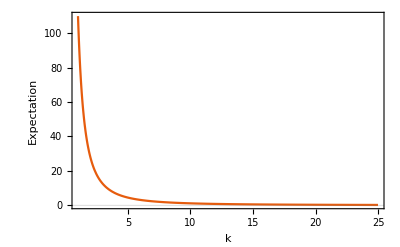

Plot::plld: {5000000,50000,50000} 中 n 的端点必须有不同的机器精度数值.

Plot[testnum[n],{n,50000,50000},PlotTheme→Scientific,FrameLabel→{样品数,确保检出检测次数},PlotLabel→组合检测法]

```mathematica
；,Null^2
```

```mathematica
Clear["Global`*"];
n=500;

Array[s,n];
Table[s[i]=0,{i,1,n}];
s[RandomInteger[{1,n}]]=1;
Sum[s[i],{i,1,n}]
Do[If[Sum[s[i],{i,1,Integer[n/2]}]==1,
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

RandomInteger::unifr: 对于离散均匀分布范围的端点，由 {1,n} 指定的端点值不是整数.

Set::pkspec1: 表达式 RandomInteger[{1,n}] 不能作为部分指定使用.

```mathematica
Clear["Global`*"];
```

```mathematica
n=50000;
d=10;
k=10
```

10

```mathematica
N[n/(k,((1+k),(1+(1-d/n)^k)+(1-d/n)^k))]
```

Piecewise[{{-141.728+175.799 (1/x^2)^(1/10)+4.88249 x, 1.≤x<5.22227}, {9.87867-0.452 x, 5.22227≤x<11.2327}, {6.752-0.167636 x, 11.2327≤x<21.0202}, {4.74333-0.07 x, 21.0202≤x<25.}, {0, True}}]

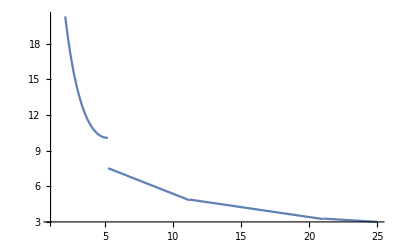

```mathematica
data={{1,40.14},{2,21.08},{1,37.84},{2,20.78},{3,14.34},{4,11.04},{5,10.02},{6,6.94},{7,7},{8,6.36},{9,5.76},{10,5.16},{11,5},{12,4.98},{13,4.66},{14,4.5},{15,3.9},{16,3.84},{17,3.78},{18,3.76},{19,3.54},{20,3.52},{21,3.38},{22,3.26},{23,3.02},{24,3.12},{25,2.88}};FindFormula[data,x]
Plot[%,{x,1,25}]
```

```mathematica
FindFit[Import["F:\\data3.txt","Table"][[All,1;;2]], (6*10^6)/(a*k((1-1/(6*10^6))^(a*k)+(a*k+1)*((1-1/(6*10^6))^(a*k)+1))),{a},k]
```

FindFit::fdssnv: 没有变量的搜索指定 116629 应该是由 1 至 4 个元素组成的列表.

FindFit[{{1,40.14},{2,21.08},{1,37.84},{2,20.78},{3,14.34},{4,11.04},{5,10.02},{6,6.94},{7,7},{8,6.36},{9,5.76},{10,5.16},{11,5},{12,4.98},{13,4.66},{14,4.5},{15,3.9},{16,3.84},{17,3.78},{18,3.76},{19,3.54},{20,3.52},{21,3.38},{22,3.26},{23,3.02},{24,3.12},{25,2.88},{{27,,3.2,},{{28,,3.,},{{29,,2.74,},{{30,,2.82,}},6000000/(116629 k ((5999999/6000000)^(116629 k)+(1+(5999999/6000000)^(116629 k)) (1+116629 k))),{116629},k]

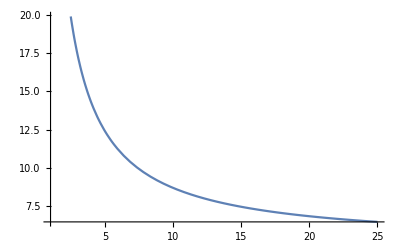

```mathematica
Plot[37/x+5,{x,1,25}]
```

```mathematica
Clear["Global`*"];
```

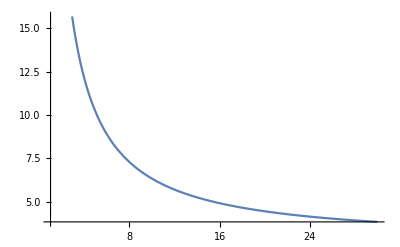

```mathematica
a1=356.82572;
a2=1.67541;
x0=0.13104;
p=1.05361;
Plot[1+a2+(a1-a2)/(1+(x/x0)^p),{x,1,30}]
```